# Notebook to Reproduce All Results/Figures for “Bivalent Impact of Social Networks on the Overarming Dilemma: Insights to Align Social and Individual Interests”

## Figure 1

```mathematica
Clear["`*"]
SetDirectory[NotebookDirectory[]];
```

```mathematica
IndS[bg_,cg_,pa_, ds_,de_,dn_]:=If[(bg-cg+de pa+dn pa)/((dn+ds) pa)>1|| (bg-cg+de pa+dn pa)/((dn+ds) pa)<0,0,(bg-cg+de pa+dn pa)/((dn+ds) pa)];
PoPS[bg_,cg_,pa_, ds_,de_,dn_]:=If[(bg-cg+2 dn pa)/(2 (dn+ds) pa)>1|| (bg-cg+2 dn pa)/(2 (dn+ds) pa)<0,0,(bg-cg+2 dn pa)/(2 (dn+ds) pa)];
```

```mathematica
f[x_,y_]:=IndS[0.1,0.15,x, 1,y,0.1]-PoPS[0.1,0.15,x, 1,y,0.1];
tableSize=100;
xMin=0.0001;xMax=1;
yMin=0.0999;yMax=1;
xstepSize=(xMax-xMin)/(tableSize-1);
ystepSize=(yMax-yMin)/(tableSize-1);
data=Table[{x,y,f[x,y]},{x,xMin,xMax,xstepSize},{y,yMin,yMax,ystepSize}];
flattenedData=Flatten[data,1];
maxValue=Max[Abs[flattenedData[[All,3]]]];
customColorFunc[z_]:=If[z==0,LightBlue,Blend[{LightBlue,Red},Abs[z]]];
fig1aa=ListContourPlot[flattenedData,PlotLegends->BarLegend[{customColorFunc,{0,1}},LabelStyle->Directive[Black,FontSize->12,FontFamily->"Helvetica"],LegendMargins->{{0,0},{0,0}},LegendMarkerSize->300,LegendLabel->"misalignment"],ColorFunction->customColorFunc,Mesh->None,Contours->20,ContourStyle->None,FrameLabel->{"Provocation rate, \!\(\*
StyleBox[SubscriptBox[\"p\", \"a\"],\nFontFamily->\"Times New Roman\",\nFontWeight->\"Regular\",\nFontSlant->\"Italic\"]\)","Concession cost, \!\(\*SubscriptBox[\(δ\), \(e\)]\)"},ImageSize->{Automatic,300},FrameTicksStyle->Directive[FontSize->20,Black],LabelStyle->Directive[FontSize->20,Black],FrameStyle->Directive[Black,Thickness[0.004]]];
fig11b=RegionPlot[IndS[0.1,0.15,x, 1,y,0.1]==0,{x,xMin,xMax},{y,yMin,yMax},PlotStyle->{LightBlue},BoundaryStyle->{Lighter[Blue,0.6]}];
fig11c=ListLinePlot[{{0.25,0},{0.25,1}},PlotStyle->{Thickness[0.01],Dashed,LightGray}];
fig1new=Show[fig1aa,fig11b,fig11c,ImageSize->300];
```

```mathematica
fig1dilemmaa=Plot[{IndS[0.1,0.15,x, 1,0.6,0.1],PoPS[.1,0.15,x, 1,0.6,0.1]},{x,0,1},Frame->True,FrameTicksStyle->Directive[20,Black],FrameLabel->{Style["Provocation rate, p_a",Black,20],Style["Gun adoption rate",Black,20]},AspectRatio->1,PlotStyle->{{Thick,Red},{Thick,Blue}},PlotRange->{0,1},PlotLegends->Placed[{"Individual optimum","Social optimum"},{Left,Top}],ImageSize->300,LabelStyle->Directive[FontSize->16,Black],FrameStyle->Directive[Black,Thickness[0.004]],LabelStyle->{FontSize->18}];
```

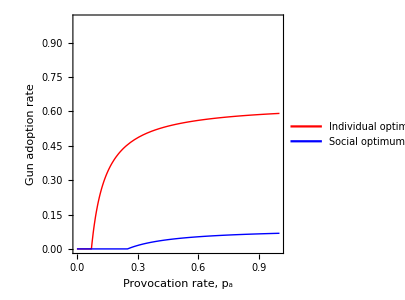

```mathematica
fig1all=GraphicsGrid[{{fig1dilemmaa,fig1new}},ImageSize->800]
```

## Figure 2

```mathematica
Clear["`*"]
SetDirectory[NotebookDirectory[]];
```

```mathematica
IndS[bg_,cg_,pa_, ds_,de_,dn_]:=If[(bg-cg+de pa+dn pa)/((dn+ds) pa)>1|| (bg-cg+de pa+dn pa)/((dn+ds) pa)<0,0,(bg-cg+de pa+dn pa)/((dn+ds) pa)];
figwm=Plot[{IndS[0.1,0.15,x, 1,0.6,0.1]},{x,0,1},Frame->True,FrameTicksStyle->Directive[20,Black],AspectRatio->1,PlotStyle->{{Gray,Dashed,Thickness[0.015]}},PlotRange->{0,1},PlotLegends->Placed[{Style["Well-mixed",FontSize->16]},{Right,Bottom}],ImageSize->300,LabelStyle->Directive[FontSize->20,Black],FrameStyle->Directive[Black,Thickness[0.004]],FrameTicksStyle->Directive[FontSize->20,Black]];
data=Import["mathematica/vonNeunambeta10.xlsx",{"Data",1}];
dataWithoutHeader=Rest[data];
xValues1=dataWithoutHeader[[All,1]];
yValues1=dataWithoutHeader[[All,2]];
```

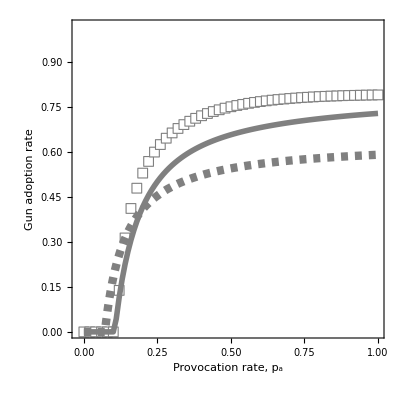

```mathematica
fig2a=ListPlot[Transpose[{xValues1,yValues1}],PlotRange->{{-0.02,1},{0,1.02}},PlotMarkers->{Graphics[{EdgeForm[Gray],White,Rectangle[]},ImageSize->10],,10.},Frame->True,PlotLegends->Placed[{Style["Lattice Simulations",FontSize->16]},{Right, Bottom}],FrameLabel->{"Provocation rate, \!\(\*
StyleBox[SubscriptBox[\"p\", \"a\"],\nFontFamily->\"Times New Roman\",\nFontWeight->\"Regular\",\nFontSlant->\"Italic\"]\)","Gun adoption rate"},ImageSize->{Automatic,300},FrameTicksStyle->Directive[FontSize->20,Black],LabelStyle->Directive[FontSize->20,Black],FrameStyle->Directive[Black,Thickness[0.004]],AspectRatio->1/GoldenRatio];
xValues2=dataWithoutHeader[[All,3]];
yValues2=dataWithoutHeader[[All,4]];
fig2c=ListPlot[Transpose[{xValues2,yValues2}],PlotRange->{{-0.01,0.41},{0,1.02}},Joined->True,PlotStyle->{Gray,Thickness[0.01]},Frame->True,PlotLegends->Placed[{Style["Lattice Theory",FontSize->16]},{Right, Bottom}],FrameLabel->{"Provocation rate, \!\(\*
StyleBox[SubscriptBox[\"p\", \"a\"],\nFontFamily->\"Times New Roman\",\nFontWeight->\"Regular\",\nFontSlant->\"Italic\"]\)","Gun adoption rate"},ImageSize->{Automatic,300},FrameTicksStyle->Directive[FontSize->20,Black],LabelStyle->Directive[FontSize->20,Black],FrameStyle->Directive[Black,Thickness[0.004]],AspectRatio->1/GoldenRatio];
fig2main=Show[fig2a,fig2c,figwm,AspectRatio->1,ImageSize->400]
```

```mathematica
data=Import["mathematica/snapshotbeta10.txt","Table"];
heatmap2=ListDensityPlot[data,InterpolationOrder->0,ColorFunction->(Blend[{Blue,Red},#]&),PlotLegends->None,FrameTicks->None];
```

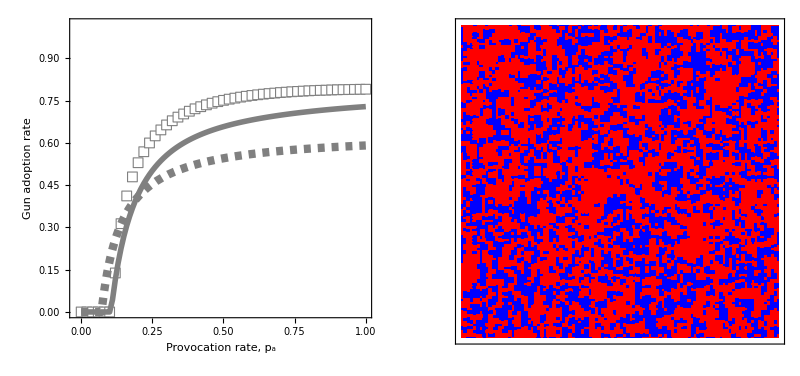

```mathematica
fig2all=GraphicsGrid[{{fig2main,heatmap2}},ImageSize->800]
```

## Figure 3

```mathematica
Clear["`*"]
SetDirectory[NotebookDirectory[]];
```

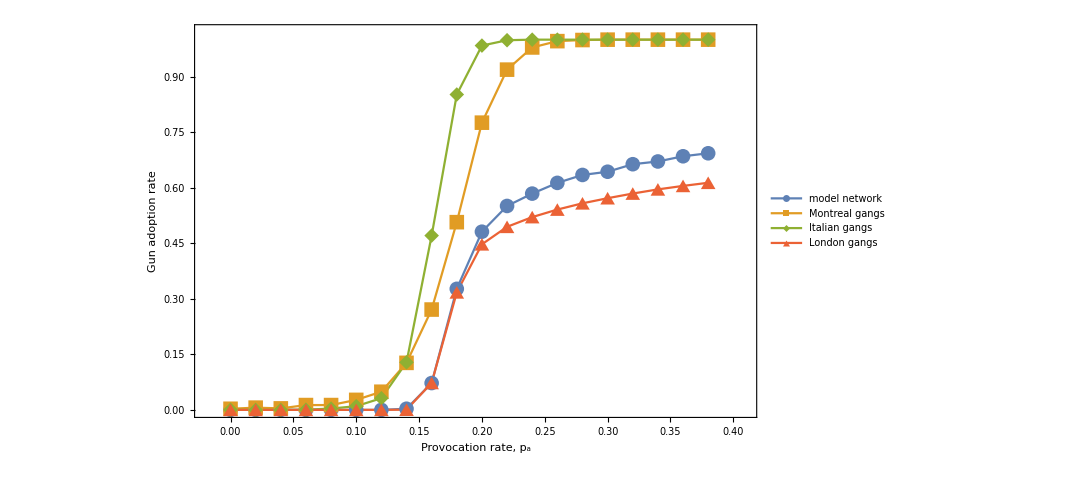

```mathematica
(*Import the data from the Excel file*)
data=Import["mathematica/realnetwork2.xlsx"];
(*Extract the relevant columns*)
xValues=data[[1,All,1]];
yValues3=data[[1,All,3]];
yValues5=data[[1,All,5]];
yValues6=data[[1,All,6]];
yValues7=data[[1,All,8]];

(*Prepare the data for plotting*)
plotData3=Transpose[{xValues,yValues3}];
plotData5=Transpose[{xValues,yValues5}];
plotData6=Transpose[{xValues,yValues6}];
plotData7=Transpose[{xValues,yValues7}];
fig3=ListPlot[{plotData3,plotData5,plotData6,plotData7},PlotRange->{{-0.02,0.41},{0,1.02}},Joined->True,PlotMarkers->{Automatic,15},Frame->True,PlotLegends->Placed[{Style["model network",FontSize->16
],Style["Montreal gangs",FontSize->16],Style["Italian gangs",FontSize->16],Style["London gangs",FontSize->16]},{Right, Bottom}],FrameLabel->{"Provocation rate, \!\(\*
StyleBox[SubscriptBox[\"p\", \"a\"],\nFontFamily->\"Times New Roman\",\nFontWeight->\"Regular\",\nFontSlant->\"Italic\"]\)","Gun adoption rate"},ImageSize->{Automatic,300},FrameTicksStyle->Directive[FontSize->25,Black],LabelStyle->Directive[FontSize->25,Black],FrameStyle->Directive[Black,Thickness[0.0022]],AspectRatio->1/GoldenRatio];
fig3main=Show[fig3,ImageSize->800]
```

## Figure 4

```mathematica
Clear["`*"]
SetDirectory[NotebookDirectory[]];
```

```mathematica
IndGraphS[k_,bg_,cg_,pa_, ds_,de_,dn_]:=If[(-((dn+ds) pa)+k (bg-cg+(de+dn) pa))/((dn+ds) (-2+k) pa)>1|| (-((dn+ds) pa)+k (bg-cg+(de+dn) pa))/((dn+ds) (-2+k) pa)<0,(Sign[(-((dn+ds) pa)+k (bg-cg+(de+dn) pa))/((dn+ds) (-2+k) pa)]+1)/2,(-((dn+ds) pa)+k (bg-cg+(de+dn) pa))/((dn+ds) (-2+k) pa)];
g[x_,y_]:=IndGraphS[4,0.1,0.15,x, 1,y,0.1];
```

```mathematica
tableSize=100;
xMin=0.0001;xMax=1;
yMin=0.10001;yMax=1;
xstepSize=(xMax-xMin)/(tableSize-1);
ystepSize=(yMax-yMin)/(tableSize-1);
data=Table[{x,y,g[x,y]},{x,xMin,xMax,xstepSize},{y,yMin,yMax,ystepSize}];
flattenedData=Flatten[data,1];
customColorFunc[z_]:=If[z==0,LightBlue,Blend[{LightBlue,Red},z]];
```

```mathematica
fig4aa=ListContourPlot[flattenedData,PlotLegends->BarLegend[{customColorFunc,{0,1}},LabelStyle->Directive[Black,FontSize->12,FontFamily->"Helvetica"],LegendMargins->{{0,0},{0,0}},LegendMarkerSize->300,LegendLabel->"gun adoption rate"],ColorFunction->customColorFunc,Mesh->None,Contours->20,ContourStyle->None,FrameLabel->{"Provocation rate, \!\(\*
StyleBox[SubscriptBox[\"p\", \"a\"],\nFontFamily->\"Times New Roman\",\nFontWeight->\"Regular\",\nFontSlant->\"Italic\"]\)","Concession cost, \!\(\*SubscriptBox[\(δ\), \(e\)]\)"},ImageSize->{Automatic,300},FrameTicksStyle->Directive[FontSize->20,Black],LabelStyle->Directive[FontSize->20,Black],FrameStyle->Directive[Black,Thickness[0.004]]];
fig4b=RegionPlot[(0.45454545454545453 (-1.1 pa+4 (-0.04999999999999999+(0.1+de) pa)))/pa<0,{pa,0,1},{de,0.1,1},PlotStyle->LightBlue,BoundaryStyle->{Lighter[Blue,0.6]}];
fig4c=ContourPlot[pa==0.09999999999999998/(-0.9+2 de),{pa,0,1},{de,0.1,1},ContourStyle->{Thickness[0.01], Dashed,LightGray}];
```

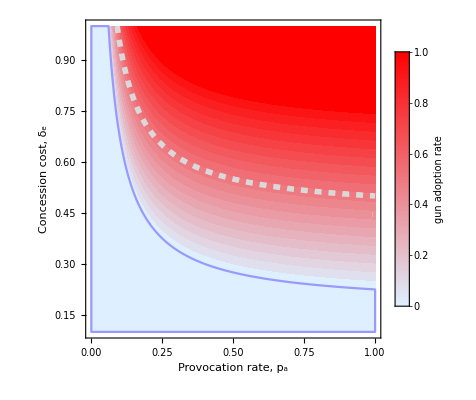

```mathematica
Figure4=Show[fig4aa,fig4b,fig4c,ImageSize->400]
```

## Figure S1

```mathematica
Clear["`*"]
SetDirectory[NotebookDirectory[]];
```

```mathematica
IndS[bg_,cg_,pa_, ds_,de_,dn_]:=If[(bg-cg+de pa+dn pa)/((dn+ds) pa)>1|| (bg-cg+de pa+dn pa)/((dn+ds) pa)<0,0,(bg-cg+de pa+dn pa)/((dn+ds) pa)];
PoPS[bg_,cg_,pa_, ds_,de_,dn_]:=If[(bg-cg+2 dn pa)/(2 (dn+ds) pa)>1|| (bg-cg+2 dn pa)/(2 (dn+ds) pa)<0,0,(bg-cg+2 dn pa)/(2 (dn+ds) pa)];
```

```mathematica
g[x_,y_]:=IndS[0.1,0.15,x, y,0.6,0.1]-PoPS[0.1,0.15,x, y,0.6,0.1];
tableSize=100;
xMin=0.0001;xMax=1;
yMin=0.60001;yMax=1;
xstepSize=(xMax-xMin)/(tableSize-1);
ystepSize=(yMax-yMin)/(tableSize-1);
data=Table[{x,y,g[x,y]},{x,xMin,xMax,xstepSize},{y,yMin,yMax,ystepSize}];
flattenedData=Flatten[data,1];
customColorFunc[z_]:=If[z==0,LightBlue,Blend[{LightBlue,Red},Abs[z]]];
fig11aS=ListContourPlot[flattenedData,ColorFunction->customColorFunc,Mesh->None,Contours->20,ContourStyle->None,FrameLabel->{"Provocation rate, \!\(\*
StyleBox[SubscriptBox[\"p\", \"a\"],\nFontFamily->\"Times New Roman\",\nFontWeight->\"Regular\",\nFontSlant->\"Italic\"]\)","Shootout cost, \!\(\*SubscriptBox[\(δ\), \(s\)]\)"},ImageSize->{Automatic,300},FrameTicksStyle->Directive[FontSize->20,Black],LabelStyle->Directive[FontSize->20,Black],FrameStyle->Directive[Black,Thickness[0.004]]];
```

```mathematica
h[x_,y_]:=IndS[0.1,0.15,x, 1,0.6,y]-PoPS[0.1,0.15,x, 1,0.6,y];
tableSize=100;
xMin=0.0001;xMax=1;
yMin=0.0001;yMax=0.6;
xstepSize=(xMax-xMin)/(tableSize-1);
ystepSize=(yMax-yMin)/(tableSize-1);
data=Table[{x,y,h[x,y]},{x,xMin,xMax,xstepSize},{y,yMin,yMax,ystepSize}];
flattenedData=Flatten[data,1];
fig11bS=ListContourPlot[flattenedData,ColorFunction->customColorFunc,Mesh->None,Contours->20,ContourStyle->None,FrameLabel->{"Provocation rate, \!\(\*
StyleBox[SubscriptBox[\"p\", \"a\"],\nFontFamily->\"Times New Roman\",\nFontWeight->\"Regular\",\nFontSlant->\"Italic\"]\)","Normal dispute cost, \!\(\*SubscriptBox[\(δ\), \(n\)]\)"},ImageSize->{Automatic,300},FrameTicksStyle->Directive[FontSize->20,Black],LabelStyle->Directive[FontSize->20,Black],FrameStyle->Directive[Black,Thickness[0.004]]];
fig11bSb2=Plot[0.025/x,{x,0,1},PlotStyle->Dashed,PlotRange->All];
fig11bSb=ContourPlot[PoPS[0.1,0.15,x, 1,0.6,y]==0,{x,xMin,xMax},{y,yMin,yMax},ContourStyle->{Dashed}];
figbsss=Show[fig11bS,fig11bSb2];
```

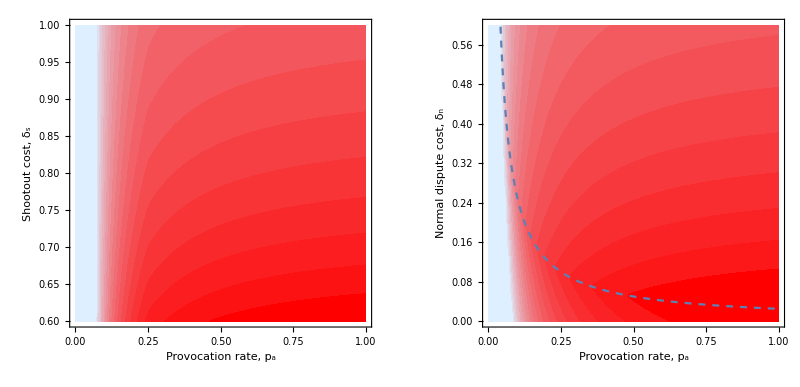

```mathematica
FigureS1=GraphicsGrid[{{fig11aS,figbsss}},ImageSize->800]
```

## Figure S2

```mathematica
Clear["`*"]
SetDirectory[NotebookDirectory[]];
```

```mathematica
data=Import["mathematica/degree.txt","Table"];
```

```mathematica
figdeg2=ListLogLogPlot[Transpose[{data[[All,1]],data[[All,2]]}],PlotStyle->Gray,PlotRange->{{1,100},{0.9,300}},Frame->True,FrameLabel->{"Number of neighbors","Number of individuals"},FrameTicksStyle->Directive[FontSize->20,Black],LabelStyle->Directive[FontSize->20,Black],ImageSize->600,AspectRatio->1,FrameStyle->Directive[Black,Thickness[0.004]]];
```

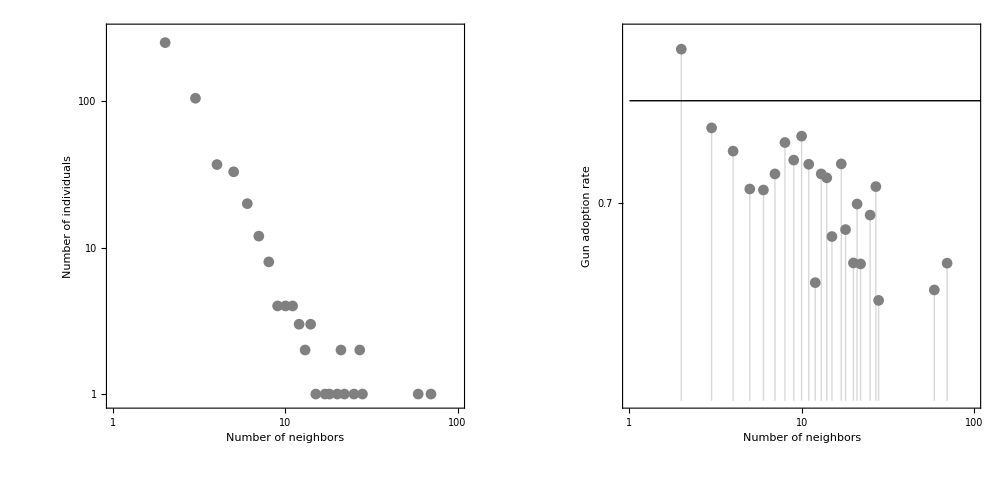

```mathematica
figdeg1=ListLogLogPlot[Transpose[{data[[All,1]],data[[All,3]]}],PlotStyle->Gray,PlotRange->{{1,100},{0.6,0.8}},Frame->True,Filling->Axis,Epilog->Line[{{Min[data[[All,1]]]-2,Log[0.758]},{Max[data[[All,1]]],Log[0.758]}}],FrameLabel->{"Number of neighbors","Gun adoption rate"},FrameTicksStyle->Directive[FontSize->20,Black],LabelStyle->Directive[FontSize->20,Black],ImageSize->600,AspectRatio->1,FrameStyle->Directive[Black,Thickness[0.004]]];
figs2=GraphicsGrid[{{figdeg2,figdeg1}},ImageSize->1000]
```

## Figure S3

```mathematica
Clear["`*"]
SetDirectory[NotebookDirectory[]];
```

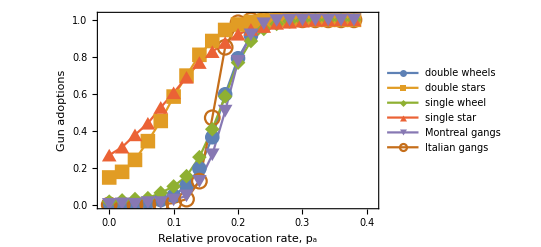

```mathematica
data=Import["mathematica/wheels.txt","Table"];
doublewheels = Transpose[{data[[All,1]],data[[All,2]]}];
doublestars = Transpose[{data[[All,1]],data[[All,3]]}];
singlewheel = Transpose[{data[[All,1]],data[[All,4]]}];
singlestar=Transpose[{data[[All,1]],data[[All,5]]}];
montreal=Transpose[{data[[All,1]],data[[All,6]]}];
italian=Transpose[{data[[All,1]],data[[All,7]]}];
figs3=ListPlot[{doublewheels,doublestars,singlewheel,singlestar,montreal,italian},PlotRange->{{-0.01,0.41},{0,1.02}},Joined->True,PlotMarkers->{Automatic,15},Frame->True,PlotLegends->Placed[{"double wheels","double stars","single wheel","single star","Montreal gangs","Italian gangs"},{Right, Bottom}],FrameLabel->{"Relative provocation rate, \!\(\*
StyleBox[SubscriptBox[\"p\", \"a\"],\nFontFamily->\"Times New Roman\",\nFontWeight->\"Regular\",\nFontSlant->\"Italic\"]\)","Gun adoptions"},ImageSize->{Automatic,400},FrameTicksStyle->Directive[FontSize->20,Black],LabelStyle->Directive[FontSize->20,Black],FrameStyle->Directive[Black,Thickness[0.004]],AspectRatio->1/GoldenRatio]
```

## Figure S4

```mathematica
Clear["`*"]
SetDirectory[NotebookDirectory[]];
```

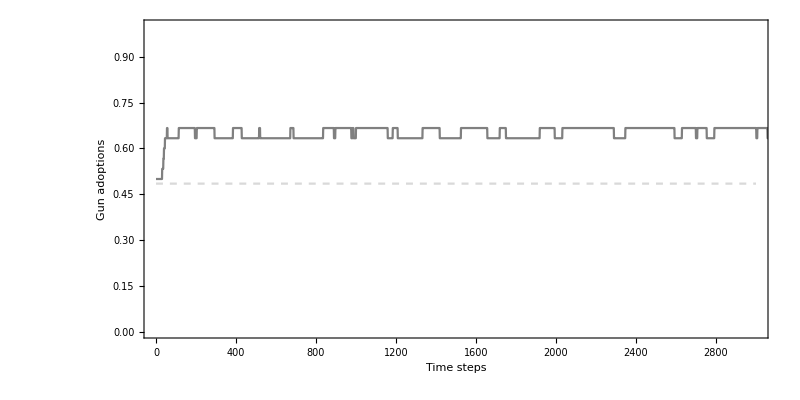

```mathematica
data=Import["mathematica/rowT00_b000_it00.txt","Table"];
figstarsim=ListPlot[data,Joined->True,PlotStyle->Gray,PlotRange->{{0,3000},{0,1}},Frame->True,FrameLabel->{"Time steps","Gun adoptions"},FrameTicksStyle->Directive[FontSize->20,Black],LabelStyle->Directive[FontSize->20,Black],ImageSize->600,AspectRatio->1/2,FrameStyle->Directive[Black,Thickness[0.002]]];
figstarsim2=ListLinePlot[{{0,0.48484848484848486},{3000,0.48484848484848486}},PlotStyle->{Dashed,LightGray}];
figs4=Show[figstarsim,figstarsim2,ImageSize->800]
```

## Figure S5

```mathematica
Clear["`*"]
SetDirectory[NotebookDirectory[]];
```

```mathematica
(*parameters used for the plots*)
bg=0.1;
cg=0.15;
 ds=1;
dn=0.1;
de=0.6;
n=29;(*n, number of leaf nodes*)
```

```mathematica
NSolve[{cg-bg==pa(de+i/n de + (n-i)/n dn)&&cg-bg==pa(2 de - i/n(ds+de))},{pa,i}];
Solve[cg-bg==pa(2 de - 0/n(ds+de)),pa];
Solve[cg-bg==pa(de+0/n de + (n-0)/n dn),pa];
figsxd=ListLinePlot[{{0.04166666666666666,0},{0.07142857142857141,0}},PlotStyle->{Gray}];
figsxe=ContourPlot[cg-bg==pa(2 de - i/n(ds+de)),{pa,0.061046511627906974,0.4},{i,0,29},ContourStyle->{Gray}];
figs1a=RegionPlot[cg-bg<pa(de+i/n de + (n-i)/n dn),{pa,0,1},{i,0,29}];
figs1b=RegionPlot[cg-bg<pa(2 de - i/n(ds+de)),{pa,0,1},{i,0,29}];
Figsxa=RegionPlot[{cg-bg<pa(de+i/n de + (n-i)/n dn)&&cg-bg>pa(2 de - i/n(ds+de))},{pa,0,0.4},{i,0,25},PlotPoints->60,PlotStyle->LightRed,BoundaryStyle->{Gray,Dashed}];
Figsxb=RegionPlot[{cg-bg<pa(de+i/n de + (n-i)/n dn)&&cg-bg<pa(2 de - i/n(ds+de))},{pa,0,0.4},{i,0,25},PlotPoints->50,PlotStyle->LightGreen,BoundaryStyle->{Gray,Dashed}];
Figsxc=RegionPlot[{cg-bg>pa(de+i/n de + (n-i)/n dn)&&cg-bg<pa(2 de - i/n(ds+de))},{pa,0,0.4},{i,0,25},PlotPoints->60,PlotStyle->LightGray,BoundaryStyle->{Gray,Dashed}];
FigSStar=Show[Figsxa,Figsxb,Figsxc,figsxe,figsxd,FrameLabel->{"Relative provocation rate, p_a","Number of A's among leaf nodes"},FrameTicksStyle->Directive[FontSize->20,Black],LabelStyle->Directive[FontSize->20,Black],ImageSize->400];
```

```mathematica
Figsxb2=RegionPlot[{cg-bg<pa(2 de - i/n(ds+de))&&pa>0.061046511627906974},{pa,0,0.4},{i,0,25},PlotPoints->50,PlotStyle->LightGreen,BoundaryStyle->{Gray,Dashed}];
Figsxc2=RegionPlot[{pa<0.061046511627906974&&cg-bg<pa(2 de - i/n(ds+de))},{pa,0,0.4},{i,0,25},PlotPoints->80,PlotStyle->LightGray,BoundaryStyle->{Gray,Dashed}];
FigSStar2=Show[Figsxa,Figsxb2,Figsxc2,figsxe,figsxd,FrameLabel->{"Relative provocation rate, p_a","Number of A's among leaf nodes"},FrameTicksStyle->Directive[FontSize->20,Black],LabelStyle->Directive[FontSize->20,Black],ImageSize->400];
```

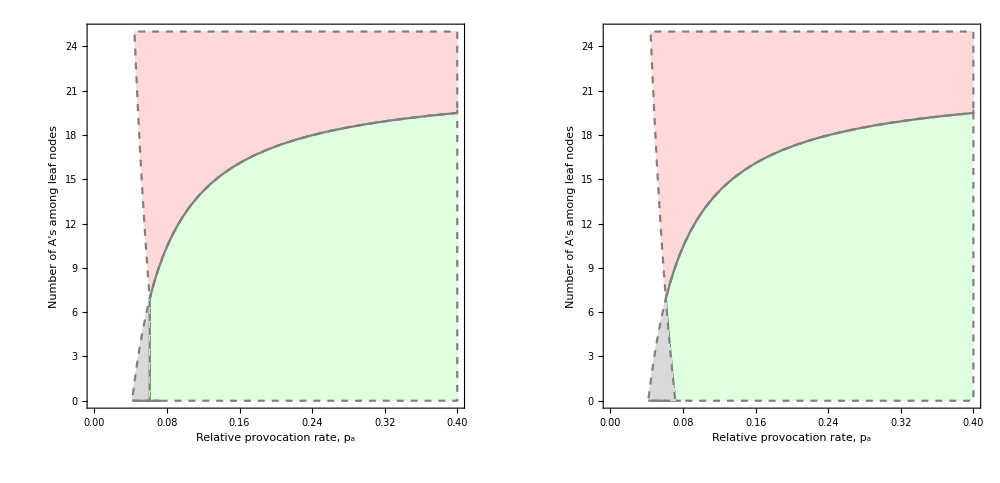

```mathematica
figs5=GraphicsGrid[{{FigSStar2,FigSStar}},ImageSize->1000]
```